# Vaje 1

1.  S  pomočjo  Mathematice  izračunaj: 
ulomki / (lahko uporabljamo TraditionalForm[`izraz`] ali shift + cmd + T)
Sin
ⅇ je esc ee esc. 
Log[b, num]

2.   Poenostavi izraze
Simplify
FullSimplify

```mathematica
Clear[x, y]
```

```mathematica
Expand[Power[(x + x * y + y), 10]]
```

x^10+10 x^9 y+10 x^10 y+45 x^8 y^2+90 x^9 y^2+45 x^10 y^2+120 x^7 y^3+360 x^8 y^3+360 x^9 y^3+120 x^10 y^3+210 x^6 y^4+840 x^7 y^4+1260 x^8 y^4+840 x^9 y^4+210 x^10 y^4+252 x^5 y^5+1260 x^6 y^5+2520 x^7 y^5+2520 x^8 y^5+1260 x^9 y^5+252 x^10 y^5+210 x^4 y^6+1260 x^5 y^6+3150 x^6 y^6+4200 x^7 y^6+3150 x^8 y^6+1260 x^9 y^6+210 x^10 y^6+120 x^3 y^7+840 x^4 y^7+2520 x^5 y^7+4200 x^6 y^7+4200 x^7 y^7+2520 x^8 y^7+840 x^9 y^7+120 x^10 y^7+45 x^2 y^8+360 x^3 y^8+1260 x^4 y^8+2520 x^5 y^8+3150 x^6 y^8+2520 x^7 y^8+1260 x^8 y^8+360 x^9 y^8+45 x^10 y^8+10 x y^9+90 x^2 y^9+360 x^3 y^9+840 x^4 y^9+1260 x^5 y^9+1260 x^6 y^9+840 x^7 y^9+360 x^8 y^9+90 x^9 y^9+10 x^10 y^9+y^10+10 x y^10+45 x^2 y^10+120 x^3 y^10+210 x^4 y^10+252 x^5 y^10+210 x^6 y^10+120 x^7 y^10+45 x^8 y^10+10 x^9 y^10+x^10 y^10

```mathematica
TrigExpand[Sin[x + y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

```mathematica
x = 1
```

1

```mathematica
x + 1
```

2

```mathematica
Clear[x];
s = {3, 2, 0, 0, 5, 13, 2, -x, 8}
```

{3,2,0,0,5,13,2,-x,8}

```mathematica
s[[-1]]
```

8

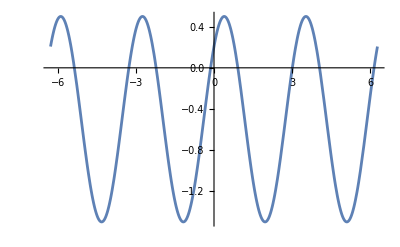

```mathematica
Plot[Sin[2x+ Pi/4] - 1/2, {x, -2Pi, 2Pi}]
```

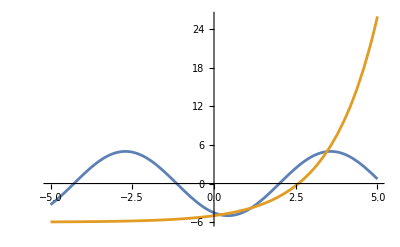

```mathematica
f[x_]:= 5 * Sin[x-2];
g[x_] := Power[2, x] - 6;
Plot[{f[x], g[x]}, {x, -5, 5}]
```

```mathematica
NSolve[{f[x] == g[x], 0 <= x <= 10}, x]
```

{{x→0.190811},{x→1.13596},{x→3.45504}}